# LinearSolve

## Basic Examples

```mathematica
b=.
```

```mathematica
d=.
```

```mathematica
x=.
```

```mathematica
LinearSolve[({{a, b}, {c, d}}),{x,y}]
```

{(d x-b y)/(-b c+a d),(c x-a y)/(b c-a d)}

With no right-hand side, a LinearSolveFunction is returned:

```mathematica
ls=LinearSolve[({{1, 2}, {3, 4}})]
```

LinearSolveFunction[…]

```mathematica
ls[{5,6}]===LinearSolve[({{1, 2}, {3, 4}}),{5,6}]
```

True

## Options

### Method

#### “Banded”

Solve m.x=b. using a banded matrix method:

```mathematica
m=SparseArray[{{i_,i_}->-2.,{i_,j_}/;Abs[i-j]==1->1.},{19999,19999}];
b=Table[0.,{19999}];
b[[9999]]=1.;
```

```mathematica
Timing[x=LinearSolve[m,b,Method->"Banded"];]
```

{0.015625,Null}

Check a relative error of the computed solution:

```mathematica
Norm[m.x-b]/Norm[x]
```

1.36698×10^-16

#### “Cholesky”

```mathematica
m=SparseArray[{{i_,i_}->2.,{i_,j_}/;Abs[i-j]==1->-1.},{19999,19999}];
b=Table[0.,{19999}];b[[9999]]=1.;
```

```mathematica
Timing[x=LinearSolve[m,b,Method->"Cholesky"];]
```

{0.046875,Null}

Check a relative error of the computed solution:

```mathematica
Norm[m.x-b]/Norm[x]
```

2.89801×10^-16

Solve m.x==b using a Krylov method:

```mathematica
m=SparseArray[{{i_,i_}->-2.,{i_,j_}/;Abs[i-j]==1->1.},{19999,19999}];
b=Table[0.,{19999}];b[[9999]]=1.;
```

```mathematica
Timing[x=LinearSolve[m,b,Method->"Krylov"];]
```

{0.03125,Null}

Check a relative error of the computed solution:

```mathematica
Norm[m.x-b]/Norm[x]
```

1.36698×10^-16

#### "Multifrontal”

Solve m.x==b using a directed multifrontal method:

```mathematica
m=SparseArray[{{i_,i_}->-2.,{i_,j_}/;Abs[i-j]==1->1.},{19999,19999}];
b=Table[0.,{19999}];b[[9999]]=1.;
```

```mathematica
Timing[x=LinearSolve[m,b,Method->"Multifrontal"];]
```

{0.03125,Null}

Check a relative error of the computed solution:

```mathematica
Norm[m.x-b]/Norm[x]
```

1.36858×10^-16

### Modulus

Find the solution x to m.x.==b  modulo 47:

```mathematica
m={{1,1,1},{1,2,3},{1,4,9}};
b={1,2,3};
LinearSolve[m,b,Modulus->47]
```

{23,2,23}

Verify the solution:

```mathematica
Mod[m.
LinearSolve[m,b,Modulus->47],47]
```

{1,2,3}

## Applications

Newton’s method for finding a root of a multivariate function:

```mathematica
f[{x_,y_,z_}]={x-Sin[y],z-Cos[y],Cos[x]Sin[z]};
J[{x_,y_,z_}]=D[f[{x,y,z}],{{x,y,z}}];
FixedPoint[(#-LinearSolve[J[#],f[#]])&,{.5,.5,.5}]
```

{1.,1.5708,0.}

Approximately solve the boundary value problem
u_xx+u=f: u(0)=u(1)=0

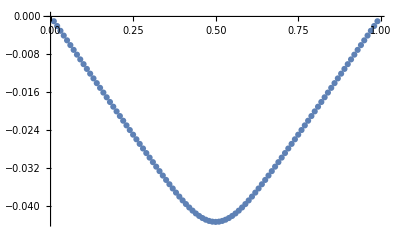

```mathematica
f[x_]:=Exp[-100(x-1/2)^2];
n=100;
h=1./n;
grid=N[Range[n-1]]/n;
s=SparseArray[{{i_,i_}->1.-2/h^2,{i_,j_}/;Abs[i-j]==1->1/h^2},{n-1,n-1}];
b=f[grid];
ux=LinearSolve[s,b];
ListPlot[Transpose[{grid,ux}]]
```

Show the error compared with the exact solution:

```mathematica
u=.
```

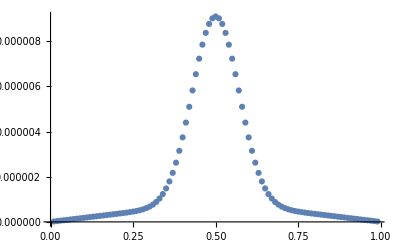

```mathematica
ex=First[u/.DSolve[{u''[x]+u[x]==f[x],u[0]==u[1]==0},u,x]][grid];
ListPlot[Transpose[{grid,Abs[ux-ex]}]]
```

## Properties & Relations

m is a 3x3 matrix:

```mathematica
m={{1,1,1},{1,0,1},{0,1,1}};
```

A system of linear equations:

```mathematica
eqns=Thread[m.{x,y,z}=={6,4,5}]
```

{x+y+z==6,x+z==4,y+z==5}

The solution computed by Solve:

```mathematica
ssol=Solve[eqns,{x,y,z}]
```

{{x→1,y→2,z→3}}

The solution computed by LinearSolve:

```mathematica
lssol=LinearSolve[m,{6,4,5}]
```

{1,2,3}

Verify that they are the same:

```mathematica
lssol==First[{x,y,z}/.ssol]
```

True

If m is nonsingular the solution of m.x=b is the inverse of m when b is the identity matrix:

```mathematica
m={{1,1,1},{1,2,3},{1,4,9}};
```

```mathematica
LinearSolve[m,IdentityMatrix[3]]==Inverse[m]
```

True

In this case there is no solution to m.x=b:

```mathematica
m={{1,2,3},{4,5,6},{7,8,9}};
```

```mathematica
b={1,-2,1};
```

```mathematica
LinearSolve[m,b]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

LinearSolve[{{1,2,3},{4,5,6},{7,8,9}},{1,-2,1}]

Use LeastSquares to minimize ‖m.x-b‖:

```mathematica
x=LeastSquares[m,b]
```

{0,0,0}

```mathematica
Norm[m.x-b]
```

√6

Compare to general minimization:

```mathematica
Minimize[Norm[m.{x1,x2,x3}-b],{x1,x2,x3}]
```

{√6,{x1→0,x2→0,x3→0}}

There are multiple solutions to m.x=0 if m is singular:

```mathematica
m={{1,2,3},{4,5,6},{7,8,9}};
```

LinearSolve only returns one solution:

```mathematica
LinearSolve[m,{0,0,0}]
```

{0,0,0}

Use NullSpace to get the complex spanning set of solutions:

```mathematica
NullSpace[m]
```

{{1,-2,1}}